## Exact Solution: Bistable spring system

The problem was reduced to

(c_o^2-v^2)/2(du/dz)^2=ψ[u].

Integrating,

```mathematica
∫(ⅆ u)/(√((1-u)^2+d^2)-lo)
```

(lo ArcTan[(-1+u)/(√(d^2-lo^2))])/(√(d^2-lo^2))+(lo ArcTan[(lo (-1+u))/(√(d^2-lo^2) √(d^2+(-1+u)^2))])/(√(d^2-lo^2))+Log[-1+√(d^2+(-1+u)^2)+u]

Converting the ArcTan terms to Log,

```mathematica
a[x_] := (-1+x)/(√(lo^2-d^2));
b[x_] := (lo (-1+x))/(√(lo^2-d^2) √(d^2+(-1+x)^2));
z[x_]:=√((co^2-v^2)/2)Log[(1-a[x])/(1+a[x])(1-b[x])/(1+b[x])(x-1+√((x-1)^2+d^2))^((2 √(lo^2-d^2))/lo)]
```

Parameters

```mathematica
lo=√2;
d=1;
co=√10;
v=2.831;
```

Inverse plot

Anti - Soliton Plot

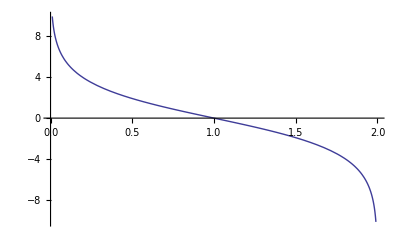

```mathematica
Plot[z[x],{x,0,2}]
```

Soliton Plot

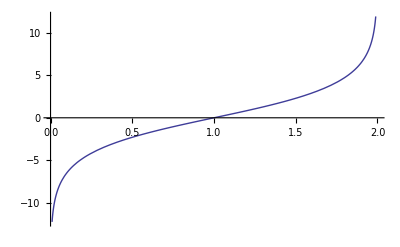

```mathematica
Plot[-z[x],{x,0,2}]
```